# Leads connected to 1 - 10 and 16 to 25

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.49,0.01]}]
```

```mathematica
leads[10]
```

{{{0.-0.848911 ⅈ,-0.499585+0. ⅈ,0.+0.170328 ⅈ,-0.00145614+0. ⅈ,0.+0.0215636 ⅈ,0.00305462+0. ⅈ,0.+0.0108578 ⅈ,-0.00416569+0. ⅈ,0.-0.000257949 ⅈ,0.00451733+0. ⅈ},8,{0.00451733+0. ⅈ,0.-0.000257949 ⅈ,-0.00416569+0. ⅈ,0.+0.0108578 ⅈ,0.00305462+0. ⅈ,0.+0.0215636 ⅈ,-0.00145614+0. ⅈ,0.+0.170328 ⅈ,-0.499585+0. ⅈ,0.-0.848911 ⅈ}},248,{{0.497586-0.230577 ⅈ,0.128014-0.288378 ⅈ,6,-0.0166891+0.015773 ⅈ,-0.0119669+0.0352477 ⅈ},{1},6,{1},{1}}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=(*leads[m][[Round[ω*100+1]]]*)Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]
```

```mathematica
Clear[dist,list]
```

```mathematica
list[upleft_,downleft_,upright_,downright_]:=Module[{},Join[Transpose[Join[{Range[1,25]},{RandomSample[Join[Table[RandomInteger[{1,12}],upleft],Table[RandomInteger[{13,25}],downleft],Table[RandomInteger[{26,50}],5]]]}]],Transpose[Join[{Range[26,50]},{RandomSample[Join[Table[RandomInteger[{1,12}],upright],Table[RandomInteger[{13,25}],downright],Table[RandomInteger[{26,50}],5]]]}]]]]
```

```mathematica
dist[diagonal_]:=dist[diagonal]=Table[Module[{x=RandomInteger[{1,diagonal}]},list[x,20-x,20-(diagonal-x),diagonal-x]],5000]
```

```mathematica
dist[20][[1]]
```

{{1,6},{2,2},{3,30},{4,43},{5,14},{6,23},{7,12},{8,24},{9,8},{10,21},{11,2},{12,32},{13,25},{14,12},{15,13},{16,32},{17,25},{18,6},{19,23},{20,9},{21,22},{22,24},{23,18},{24,42},{25,22},{26,24},{27,12},{28,39},{29,14},{30,24},{31,5},{32,50},{33,1},{34,49},{35,16},{36,19},{37,12},{38,12},{39,23},{40,16},{41,5},{42,33},{43,14},{44,15},{45,40},{46,5},{47,19},{48,14},{49,24},{50,9}}

```mathematica
Manipulate[Show[ListPlot[dist[20][[v]]],ListLinePlot[Table[{x,25},{x,0,50}],PlotStyle->Red],ListLinePlot[Table[{25,x},{x,0,50}],PlotStyle->Red],ListLinePlot[Table[{x,12},{x,0,50}],PlotStyle->Red]]
,{v,Range[1,5000,1]}]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,16,25}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[16;;25,16;;25]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=10},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
device1[1][[1,1]]
```

0.376543-0.675031 ⅈ

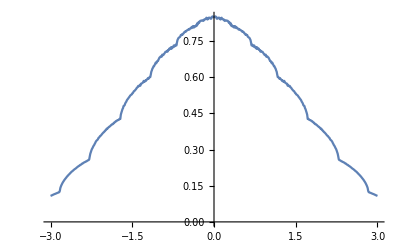

```mathematica
ListLinePlot[Table[{ω,-Im[LEFT[ω,10][[10,10]]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
dist[20][[1]]
```

{{1,16},{2,20},{3,18},{4,19},{5,37},{6,22},{7,15},{8,19},{9,17},{10,17},{11,5},{12,14},{13,16},{14,25},{15,44},{16,27},{17,21},{18,19},{19,15},{20,16},{21,15},{22,44},{23,22},{24,28},{25,25},{26,14},{27,16},{28,35},{29,16},{30,21},{31,18},{32,13},{33,10},{34,15},{35,17},{36,30},{37,14},{38,30},{39,24},{40,15},{41,18},{42,41},{43,21},{44,15},{45,47},{46,18},{47,23},{48,19},{49,15},{50,14}}

```mathematica
TLD[1]
```

```mathematica
CA[ω_,ϵ1_,diagonal_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J= device1[ω]},
Do[
J=Inverse[IdentityMatrix[50]-Inverse[Module[{κ=β[ω,0.0001,1,0,50],n= dist[diagonal][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].T[1,50].J.T[1,50]].Inverse[Module[{κ=β[ω,0.0001,1,0,50],n= dist[diagonal][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,50}];J=J];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
CA[1,1,5,1]//MatrixForm
```

2.37973

```mathematica
Mean[ParallelTable[CA[1,1,10,n],{n,2000}]]//AbsoluteTiming
```

{41.3675,2.36442}

```mathematica
ggg[diagonal_]:=Export["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_"<>ToString[diagonal]<>"_ϵ1_leads_16_25.dat",Table[{ω,Mean[ParallelTable[CA[ω,1,diagonal,NUM],{NUM,1000}]]},{ω,Range[-3,3,0.01]}]]
```

```mathematica
Table[Print[x];ggg[x],{x,Range[5,20,1]}]
```

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_5_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_6_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_7_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_8_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_9_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_10_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_11_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_12_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_13_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_14_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_15_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_16_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_17_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_18_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_19_ϵ1_leads_16_25.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_20_ϵ1_leads_16_25.dat}

```mathematica
transmission = Table[{x,Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_"<>ToString[x]<>"_ϵ1_leads_16_25.dat"]},{x,Range[5,20,1]}]
```

{{5,{{-3.,1.26338},{-2.99,1.23105},{-2.98,1.07243},{-2.97,0.921735},{-2.96,1.0526},{-2.95,1.20893},{-2.94,1.46336},{-2.93,1.13627},{-2.92,1.2098},{-2.91,0.948835},{-2.9,0.8351},{-2.89,1.02568},{-2.88,1.08853},576,{2.89,0.865217},{2.9,0.835072},{2.91,0.816064},{2.92,0.859874},{2.93,0.905338},{2.94,0.884949},{2.95,0.999557},{2.96,1.04796},{2.97,0.944563},{2.98,0.973212},{2.99,0.922606},{3.,0.873603}}},14,{20,{1}}}
 |  |  |  |

```mathematica
input = Table[ParallelTable[{ω,CA[ω,1,18,NUM]},{ω,Range[-3,3,0.01]}],{NUM,Range[2000,2100,1]}]
```

{{{-3.,1.65038},{-2.99,1.07969},{-2.98,1.04628},{-2.97,1.07463},{-2.96,1.4968},{-2.95,1.06847},{-2.94,1.6821},{-2.93,0.709326},{-2.92,1.16783},{-2.91,0.998104},{-2.9,1.3435},{-2.89,0.910178},{-2.88,0.868885},575,{2.88,0.269154},{2.89,1.22215},{2.9,0.147223},{2.91,0.963486},{2.92,0.105803},{2.93,1.12861},{2.94,1.15999},{2.95,1.25816},{2.96,1.2804},{2.97,0.717486},{2.98,1.05506},{2.99,0.323031},{3.,0.877413}},99,{1}}
 |  |  |  |

```mathematica
Dimensions[transmission]
```

{16,2}

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;601]][[;;,1]],(m5[[1;;601,2]]-transmission[[con,2]][[1;;601,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)+NIntegrate[Interpolation[B1][ω],{ω,-y,-x}]/((-x+y)*100)]},{con,16}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Table[Abs[misfit[3,0.5,n][[2]][[1]]-18]/18,{n,100}]
```

{7/18,1/18,2/9,5/9,1/18,1/9,2/9,1/6,1/18,1/18,1/9,1/9,1/9,1/18,2/9,1/18,1/9,1/18,1/18,0,1/9,1/9,1/9,0,1/18,1/9,1/9,0,1/18,1/18,1/9,2/9,1/9,1/18,1/9,1/9,0,1/9,1/18,1/9,1/18,1/6,1/9,1/9,1/9,1/18,1/6,1/9,1/9,1/6,1/18,1/18,1/9,1/9,1/9,1/9,1/3,1/18,1/18,0,1/9,1/18,0,1/18,1/9,2/9,1/9,5/18,5/18,1/9,1/18,1/18,1/3,1/18,1/9,0,1/18,7/18,1/9,1/18,1/18,1/9,1/18,5/9,0,2/9,0,1/6,1/18,2/9,1/18,1/9,1/9,1/6,5/18,1/9,0,1/9,1/9,5/18}

```mathematica
Mean[%84]
```

3/25

```mathematica
N[3/25]
```

0.12

```mathematica
N[87/500]
```

0.174

```mathematica
N[53/200]
```

0.265

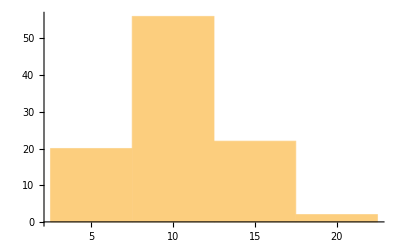

```mathematica
Histogram[%55]
```

```mathematica
Tally[%216]
```

{{8,22},{12,28},{16,29},{4,21}}

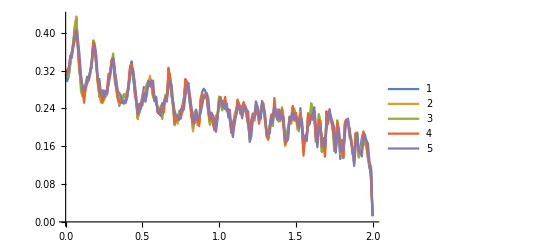

```mathematica
ListLinePlot[transmission1,PlotLegends->Placed[Automatic,Above]]
```

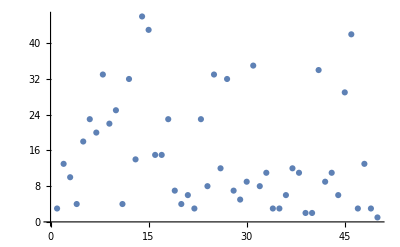

```mathematica
ListPlot[dist[10][[1]]]
```